# Algorithmic Differentiation for Matrix Polynomials

## Matrix Polynomials

A matrix polynomial of a square matrix A is the sum
	P(A)=∑_(i=1)^n α_i A^(i-1)
for an n vector (α_1,α_2,…,α_n).  The function MP below computes a matrix polynomial.

```mathematica
MP[A_,αs_]:=Module[
{n=Length[αs],CMat,Id},
Id=IdentityMatrix[Length[A]];
CMat=αs⟦n⟧ Id;
Do[
CMat=A.CMat+αs⟦i⟧ Id,
{i,n-1,1,-1}];
CMat
]
```

## Algorithmic Differentiation Big Picture

Differentiation is all about linear approximation.  The Taylor Series for a function f(x) is 
	f(x_0+h dx)≈f(x_0)+h Df(x_0).dx+h^2/2 DDf(x_0).dx.dx+…
If f:ℝ^m→ℝ^m then the derivative Df(x_0)∈ℝ^(m×m) and the second derivative DDf(x_0) is worse! Algorithmic Differentiation (AD) is a way to compute automatically compute useful derivatives.

If I have a function f:ℝ^(m×n)→ℝ^(m×n) and a smooth matrix function A:ℝ→ℝ^(m×n) then 
	t→g(t)=f(A(t)) 
is a function from ℝ→ℝ^(m×n) with linear approximation 
	g(t+h)≈f(A(0))+h Df(A(0)).A'(0) 
Forward mode AD is a set of tools to efficiently compute f(A(0)) and Df(A(0)).A'(0) at the same time.  For
	f:ℝ^(m×n)→ℝ^(m×n)
the input for our AD computation is A∈ℝ^(m×n) and dA∈ℝ^(m×n). The output is f(A)∈ℝ^(m×n) and Df(A).dA∈ℝ^(m×n).

## Algorithmic Differentiation Matrix Polynomial

The function MP below computes the matrix polynomial 
	P(A)=∑_(i=1)^n α_i A^(i-1)
and the directional derivative
	∂_dA P(A)=∑_(i=1)^n α_i(i-1)A^(i-2).dA 
at the same time.

```mathematica
MPAD[A_,dA_,αs_]:=Module[
{n=Length[αs],CMat,dCMat,Id},
Id=IdentityMatrix[Length[A]];
dCMat=0.0*Id;  (* New *)
CMat=αs⟦n⟧ Id;
Do[
dCMat=dA.CMat+A.dCMat;
CMat=A.CMat+αs⟦i⟧ Id,  (* New *)
{i,n-1,1,-1}];
{CMat, dCMat}
]
```

This looks like magic so we should check it works.

```mathematica
m=3;
{A,dA}=RandomReal[{-1,1},{2,m,m}];
αs={1,2,3};
{fA,DfA}=MPAD[A,dA,αs];
TabView[{Plot[{ Norm[MP[A+h dA,αs]-(fA+h DfA)],h^2},{h,0,1},PlotLegends->{"||f(A + h dA)-(fA + h DfA)||","h^2"}],
LogLogPlot[ {Norm[MP[A+h dA,αs]-(fA+h DfA)],h^2},{h,0,1},
PlotLegends->{"||f(A + h dA)-(fA + h DfA)||","h^2"}]
}]
```

12

## Algorithmic Differentiation Singular Value Decomposition

The same idea should work on the SVD
	A=U.S.Vᵀ
differentiating gives
	dA=dU.S.Vᵀ+U.dS.Vᵀ+U.S.dVᵀ.
Since U and V are orthogonal multiplying by Uᵀ and V gives
	Uᵀ.dA.V=Uᵀ.dU.S+dS+S.dVᵀ.V
The blue bits are known.  Our goal is to compute the other bits.

Since 
	Uᵀ.U=Id_m  and Vᵀ.V=Id_n
we must have 
	dUᵀ.U+Uᵀ.dU=0  and dVᵀ.V+Vᵀ.dV=0 .  
In other words 
	X=Uᵀ.dU  and Y=Vᵀ.dV
are skew matrices satisfying Xᵀ=-X and Yᵀ=-Y.  We want so solve 
	Uᵀ.dA.V=X.S+dS-S.Y

This is easier than it looks. Since X and Y have zeros on their diagonals (they are skew) the column and row scalings X.S and S.Y (remember S is diagonal) also have zero diagonals! So we know that dS is just the diagonal entries of the known matrix Uᵀ.dA.V . The easiest way to write this is
	dS=Id∘(Uᵀ.dA.V)
where Id is the identity matrix and ∘ is the Hadamard product (G∘H)_ij=G_ij H_ij.  Working out recipes for X and Y is a little bit more complicated so we settle for the sensitivities on the singular values given just above.

```mathematica
m=5;
{A,dA}=RandomReal[{-1,1},{2,m,m}];
{U,S,V}=SingularValueDecomposition[A];
ds=Diagonal[Uᵀ.dA.V];
s=Diagonal[S];
TabView[{
Plot[ {Norm[SingularValueList[A+ h dA]-(s+h ds)],h^2},
{h,0,0.2}],
LogLogPlot[ {Norm[SingularValueList[A+ h dA]-(s+h ds)],h^2},
{h,0,0.2}]
}]
```

12

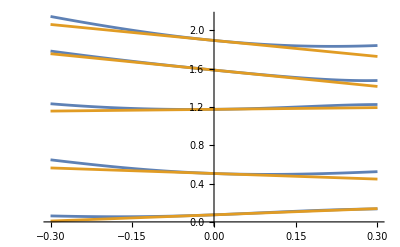

```mathematica
Plot[{
SingularValueList[A+ h dA],
s+h ds},
{h, -0.3,0.3}]
```

This looks like magic so we should check it works.

```mathematica
m=3;
{A,dA}=RandomReal[{-1,1},{2,m,m}];
αs={1,2,3};
{fA,DfA}=MPAD[A,dA,αs];
TabView[{Plot[{ Norm[MP[A+h dA,αs]-(fA+h DfA)],h^2},{h,0,1},PlotLegends->{"||f(A + h dA)-(fA + h DfA)||","h^2"}],
LogLogPlot[ {Norm[MP[A+h dA,αs]-(fA+h DfA)],h^2},{h,0,1},
PlotLegends->{"||f(A + h dA)-(fA + h DfA)||","h^2"}]
}]
```

12